```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
g = Import["citation_network.gml"];
```

```mathematica
outStubs=VertexOutDegree[g];
inStubs = VertexInDegree[g];
vertexlist=Range[VertexCount[g]];
edgelist={};
For[i=1,i≤EdgeCount[g],i++,
source = RandomSample[outStubs->vertexlist,1][[1]];
target = RandomSample[inStubs->vertexlist,1][[1]];
outStubs[[source]]-=1;
inStubs[[target]]-=1;
AppendTo[edgelist,source->target];]
```

```mathematica
degMimic=Graph[vertexlist,edgelist,ImageSize->Full];
random = RandomGraph[{VertexCount[g],EdgeCount[g]},DirectedEdges->True];
```

```mathematica
Clear[sciMet,zewail]
sciMet = Import["sciMet_dataset.gml"]
zewail= Import["zewail_dataset.gml"]
```

-Graphics-

-Graphics-

```mathematica
parents = Position[VertexOutDegree[g], _?(#>0&)] // Flatten;
popular = Position[VertexInDegree[g], _?(#>1&)] // Flatten;
pruned= Subgraph[g, Union[parents, popular],Options[g],VertexSize->Large];
prunedU = UndirectedGraph[pruned, Options[pruned]];
prunedCC =Subgraph[pruned,WeaklyConnectedComponents[pruned][[1]],Options[pruned],ImageSize->Full];
```

```mathematica
partition = FindGraphPartition[prunedCC,2];
gA = Subgraph[prunedCC, partition[[1]], Options[prunedCC],VertexSize->Large,ImageSize->Full];
gB = Subgraph[prunedCC, partition[[2]], Options[prunedCC],VertexSize->Large];
```

```mathematica
Show[g,ImageSize->Medium]
```

-Graphics-

```mathematica
printStats[degMimic_]:=
Print[VertexCount[degMimic],"\n",EdgeCount[degMimic],"\n",
EdgeCount[degMimic]/VertexCount[degMimic]//N,"\n",
GraphDiameter[UndirectedGraph[Subgraph[degMimic,WeaklyConnectedComponents[degMimic][[1]]]]],"\n",
Length[WeaklyConnectedComponents[degMimic]],"\n",
Length[Position[VertexOutDegree[degMimic], _?(#>0&)] // Flatten]/
VertexCount[degMimic]//N,"\n",
Length[VertexList[Subgraph[degMimic,WeaklyConnectedComponents[degMimic][[1]]]]]/Length[VertexList[degMimic]]//N,"\n",
GraphAssortativity[ReverseGraph[degMimic]]//N,"\n",
GraphAssortativity[degMimic]//N]
printStats[gMinus]
```

UndirectedGraph::graph: A graph object is expected at position 1 in UndirectedGraph[Subgraph[gMinus,gMinus]].

GraphDiameter::graph: A graph object is expected at position 1 in GraphDiameter[UndirectedGraph[Subgraph[gMinus,gMinus]]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Subgraph[gMinus,gMinus]].

GraphAssortativity::graph: A graph object is expected at position 1 in GraphAssortativity[ReverseGraph[gMinus]].

VertexCount[gMinus]
EdgeCount[gMinus]
EdgeCount[gMinus]/VertexCount[gMinus]
GraphDiameter[UndirectedGraph[Subgraph[gMinus,gMinus]]]
1
0.
1.
GraphAssortativity[ReverseGraph[gMinus]]
GraphAssortativity[gMinus]

```mathematica
printStats[gPMinus]
```

UndirectedGraph::graph: A graph object is expected at position 1 in UndirectedGraph[Subgraph[gPMinus,gPMinus]].

GraphDiameter::graph: A graph object is expected at position 1 in GraphDiameter[UndirectedGraph[Subgraph[gPMinus,gPMinus]]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Subgraph[gPMinus,gPMinus]].

GraphAssortativity::graph: A graph object is expected at position 1 in GraphAssortativity[ReverseGraph[gPMinus]].

VertexCount[gPMinus]
EdgeCount[gPMinus]
EdgeCount[gPMinus]/VertexCount[gPMinus]
GraphDiameter[UndirectedGraph[Subgraph[gPMinus,gPMinus]]]
1
0.
1.
GraphAssortativity[ReverseGraph[gPMinus]]
GraphAssortativity[gPMinus]

```mathematica
gPMinus = VertexDelete[prunedCC,{1,66}];
```

VertexDelete::inv: The argument {1,66} in VertexDelete[Graph[<0>, <0>], {1, 66}] is not a valid vertex.

```mathematica
modgraphs = {g, prunedCC, sciMet, zewail, random, degMimic,VertexDelete[prunedCC,1],VertexDelete[prunedCC,66],VertexDelete[prunedCC,{1,66}]};
modnames = {"$G$", "$G_p$","sciMet", "zewail","$R$", "$R_d$","gPMinus"};
```

VertexDelete::inv: The argument 1 in VertexDelete[Graph[<0>, <0>], 1] is not a valid vertex.

VertexDelete::inv: The argument 66 in VertexDelete[Graph[<0>, <0>], 66] is not a valid vertex.

VertexDelete::inv: The argument {1,66} in VertexDelete[Graph[<0>, <0>], {1, 66}] is not a valid vertex.

General::stop: Further output of VertexDelete::inv will be suppressed during this calculation.

```mathematica
For[i=3,i≤4,i++,
Print["\n",modnames[[i]]];
wrongside =0;
Print[VertexCount[modgraphs[[i]]]];
methods={"Modularity","Hierarchical","Spectral","Centrality","VertexMoving"};
For[j=1,j≤Length[methods],j++,
Print[methods[[j]],", ", Length[FindGraphCommunities[modgraphs[[i]],Method->methods[[j]]]]]
]
]
```

sciMet

1094

Modularity, 1094

Hierarchical, 1094

Spectral, 1

Centrality, 1093

VertexMoving, 1093

zewail

3147

Modularity, 3147

```mathematica
For[j=1,j≤Length[gcommunities],j++,
If[Length[gcommunities[[j]]]>1,Print[gcommunities[[j]]]]
];
```

```mathematica
i=9;
wrongside =0;
gpartition = FindGraphPartition[modgraphs[[i]]];
gcommunities = FindGraphCommunities[modgraphs[[i]]];
```

```mathematica
For[j=1,j≤Length[gcommunities],j++,
sideA =Length[Intersection[gpartition[[1]],gcommunities[[j]]]];
sideB =Length[Intersection[gpartition[[2]],gcommunities[[j]]]];
If[sideA≥sideB,wrongside+=sideB];
If[sideA<sideB,wrongside+=sideA];
];
nverts = VertexCount[modgraphs[[i]]];
Print[ Length[gcommunities], " & ", wrongside, " & ", nverts, " & ", wrongside/nverts//N]
```

18 & 114 & 1060 & 0.107547

```mathematica
CommunityGraphPlot[prunedCC,FindGraphCommunities[prunedCC];
```

```mathematica
communities = FindGraphCommunities[prunedCC];
For[i=1,i≤Length[communities],i++,
Print["Community ", i, ", size ", Length[communities[[i]]], ": ", Length[Intersection[partition[[1]],communities[[i]]]], " - ",
Length[Intersection[partition[[2]], communities[[i]]]]]]
```

Community 1, size 248: 246 - 2

Community 2, size 166: 0 - 166

Community 3, size 166: 8 - 158

Community 4, size 148: 120 - 28

Community 5, size 55: 19 - 36

Community 6, size 47: 18 - 29

Community 7, size 31: 1 - 30

Community 8, size 30: 30 - 0

Community 9, size 27: 0 - 27

Community 10, size 24: 19 - 5

Community 11, size 21: 21 - 0

Community 12, size 20: 0 - 20

Community 13, size 16: 16 - 0

Community 14, size 15: 14 - 1

Community 15, size 8: 0 - 8

Community 16, size 5: 0 - 5

Community 17, size 3: 3 - 0

```mathematica
vertices = {1,3,97,26,29,39,43,49,53,66,71,74,80,82,59,90,98,103,114,115,5,123,135,193,268,320,348,350,352,353,356,357,360,564,770,772,842,868,874,1198,1310,1316,1419,2015,2140,2432,2577,2593,2631,3025,3158,3175,3230,3398,4094,4217,4655,4679,4962,5345};
```

```mathematica
colorlabels = {};
For[i=1,i≤Length[vertices],i++,
If[MemberQ[VertexList[gA],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightGreen,EdgeForm[None]]]];
If[MemberQ[VertexList[gB],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightBlue,EdgeForm[None]]]];]
```

```mathematica
layout ={"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5};
labels = Table[vertices[[i]]->Placed[Pane[Style[PropertyValue[{g,vertices[[i]]},"title"],LineSpacing->{1,0}],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}];
```

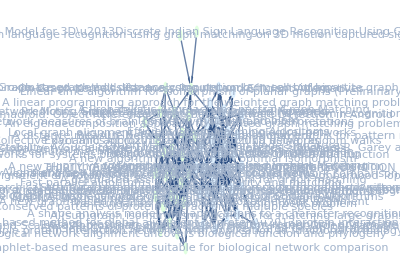

```mathematica
toRead =Graph[Subgraph[g, vertices, Options[g]],VertexStyle->colorlabels,GraphLayout->layout,EdgeStyle->Arrowheads[Medium],VertexSize->{"Nearest",0.8},VertexLabels->labels,AspectRatio->0.7,ImageSize->Full];
Show[toRead]
```

Repeat this for highlightvert = 1 (fifty years) and 66 (thirty years)

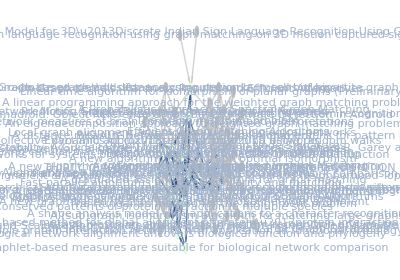

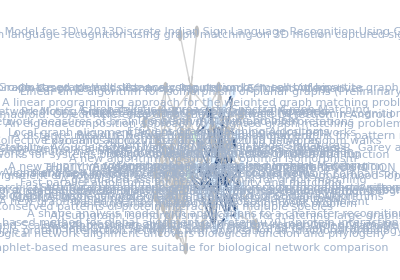

```mathematica
Show[HighlightGraph[toRead,NeighborhoodGraph[Subgraph[g, vertices ],1],GraphHighlightStyle->"DehighlightGray"]]
Show[HighlightGraph[toRead,NeighborhoodGraph[Subgraph[g, vertices ],66],GraphHighlightStyle->"DehighlightGray"]]
```